

```mathematica
g=CompleteGraph[3]
```

```mathematica
A=AdjacencyMatrix[g]//MatrixForm
```

(0 | 1 | 1
1 | 0 | 1
1 | 1 | 0)

```mathematica
L0= KirchhoffMatrix[g]
```

SparseArray[…]

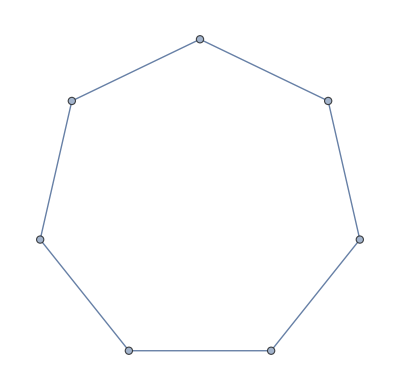

```mathematica
B=CycleGraph[7]
```

The spectrum of the undeformed Laplacian:

```mathematica
Eigenvalues[L0]
```

{3,3,0}

Now we deform L0 with the Morse function f(A)=0, F(B)=1, F(C)=1, f(1)=2, f(2)=1, f(3)=1.

```mathematica
T=KirchhoffMatrix[B]
```

SparseArray[…]

```mathematica
Eigenvalues[T]
```

{Root[-7+14 #1-7 #1^2+#1^3&,3],Root[-7+14 #1-7 #1^2+#1^3&,3],Root[-7+14 #1-7 #1^2+#1^3&,2],Root[-7+14 #1-7 #1^2+#1^3&,2],Root[-7+14 #1-7 #1^2+#1^3&,1],Root[-7+14 #1-7 #1^2+#1^3&,1],0}

```mathematica
Eigenvalues[T]
```

{Root[-7+14 #1-7 #1^2+#1^3&,3],Root[-7+14 #1-7 #1^2+#1^3&,3],Root[-7+14 #1-7 #1^2+#1^3&,2],Root[-7+14 #1-7 #1^2+#1^3&,2],Root[-7+14 #1-7 #1^2+#1^3&,1],Root[-7+14 #1-7 #1^2+#1^3&,1],0}

```mathematica
Q=CharacteristicPolynomial[T,x]
```

-49 x+196 x^2-294 x^3+210 x^4-77 x^5+14 x^6-x^7

```mathematica
Roots[Q==0,x]
```

x==0||x==1/3 (7+7^(2/3)/(1/2 (-1+3 ⅈ √3))^(1/3)+(7/2 (-1+3 ⅈ √3))^(1/3))||x==1/3 (7+7^(2/3)/(1/2 (-1+3 ⅈ √3))^(1/3)+(7/2 (-1+3 ⅈ √3))^(1/3))||x==7/3-(7^(2/3) (1+ⅈ √3))/(3 2^(2/3) (-1+3 ⅈ √3)^(1/3))-1/6 (1-ⅈ √3) (7/2 (-1+3 ⅈ √3))^(1/3)||x==7/3-(7^(2/3) (1+ⅈ √3))/(3 2^(2/3) (-1+3 ⅈ √3)^(1/3))-1/6 (1-ⅈ √3) (7/2 (-1+3 ⅈ √3))^(1/3)||x==7/3-(7^(2/3) (1-ⅈ √3))/(3 2^(2/3) (-1+3 ⅈ √3)^(1/3))-1/6 (1+ⅈ √3) (7/2 (-1+3 ⅈ √3))^(1/3)||x==7/3-(7^(2/3) (1-ⅈ √3))/(3 2^(2/3) (-1+3 ⅈ √3)^(1/3))-1/6 (1+ⅈ √3) (7/2 (-1+3 ⅈ √3))^(1/3)

```mathematica
FactorList[Q]
```

{{-1,1},{x,1},{-7+14 x-7 x^2+x^3,2}}

```mathematica
MN=DiagonalMatrix[{1,Exp[-s], Exp[-s]}]
```

{{1,0,0},{0,ⅇ^-s,0},{0,0,ⅇ^(-2 s)}}

```mathematica
MP=DiagonalMatrix[{1,Exp[s], Exp[s]}]
```

{{1,0,0},{0,ⅇ^s,0},{0,0,ⅇ^(2 s)}}

```mathematica
DL=MN.L0.MP//MatrixForm
```

(2 | -ⅇ^s | -ⅇ^(2 s)
-ⅇ^-s | 2 | -ⅇ^s
-ⅇ^(-2 s) | -ⅇ^-s | 2)

```mathematica
Eigenvalues[DL]
```

{0,3,3}

Odd Laplacian computation:

```mathematica
IN={{0,-1,-1},{-1,0,1},{1,1,0}}
```

{{0,-1,-1},{-1,0,1},{1,1,0}}

```mathematica
EVENLAP= IN. Transpose[IN]//MatrixForm
```

(2 | -1 | -1
-1 | 2 | -1
-1 | -1 | 2)

```mathematica
ODDLAP=Transpose[IN].IN
```

{{2,1,-1},{1,2,1},{-1,1,2}}

```mathematica
EN=DiagonalMatrix[{Exp[-s],Exp[-s],Exp[-2s]}]
```

{{ⅇ^-s,0,0},{0,ⅇ^-s,0},{0,0,ⅇ^(-2 s)}}

```mathematica
EP=DiagonalMatrix[{Exp[s],Exp[s], Exp[2s]}]//MatrixForm
```

(ⅇ^s | 0 | 0
0 | ⅇ^s | 0
0 | 0 | ⅇ^(2 s))

```mathematica
DODD=EN.ODDLAP.EP//MatrixForm
```

(2 | 1 | -ⅇ^s
1 | 2 | ⅇ^s
-ⅇ^-s | ⅇ^-s | 2)

```mathematica
Eigenvalues[DODD]
```

{0,3.,3.}

```mathematica
DD=MN.IN.MP
```

MN.IN.MP

```mathematica
DLAP=DD.Transpose[DD]
```

{{ⅇ^34+ⅇ^68,-ⅇ^51,-1},{-ⅇ^51,1/ⅇ^34+ⅇ^34,-1/ⅇ^51},{-1,-1/ⅇ^51,1/ⅇ^68+1/ⅇ^34}}

```mathematica
MatrixForm[DLAP]
```

(ⅇ^34+ⅇ^68 | -ⅇ^51 | -1
-ⅇ^51 | 1/ⅇ^34+ⅇ^34 | -1/ⅇ^51
-1 | -1/ⅇ^51 | 1/ⅇ^68+1/ⅇ^34)

```mathematica
Eigenvalues[DLAP]
```

{(1+2 ⅇ^34+2 ⅇ^102+ⅇ^136+√(1+4 ⅇ^34-4 ⅇ^102-2 ⅇ^136-4 ⅇ^170+4 ⅇ^238+ⅇ^272))/(2 ⅇ^68),(2 (ⅇ^68+2 ⅇ^102+3 ⅇ^136+2 ⅇ^170+ⅇ^204))/(ⅇ^68 (1+2 ⅇ^34+2 ⅇ^102+ⅇ^136+√(1+4 ⅇ^34-4 ⅇ^102-2 ⅇ^136-4 ⅇ^170+4 ⅇ^238+ⅇ^272))),0}

```mathematica
NullSpace[DLAP]
```

{{1/ⅇ^34,1/ⅇ^17,1}}

```mathematica
DODDLAP=Transpose[DD].DD//MatrixForm
```

(1/ⅇ^68+1/ⅇ^34 | 1/ⅇ^51 | -1
1/ⅇ^51 | 1/ⅇ^34+ⅇ^34 | ⅇ^51
-1 | ⅇ^51 | ⅇ^34+ⅇ^68)

```mathematica
NullSpace[DODDLAP]
```

{{ⅇ^34,-ⅇ^17,1}}

```mathematica
M={{3,-1,-1,-1,0,0,0,0},{-1,3,-1,-1,0,0,0,0},{-1,-1,3,-1,0,0,0,0},{-1,-1,-1,4,-1,0,0,0},{0,0,0,-1,4,-1,-1,-1},{0,0,0,0,-1,3,-1,-1},{0,0,0,0,-1,-1,3,-1},{0,0,0,0,-1,-1,-1,3}}
```

{{3,-1,-1,-1,0,0,0,0},{-1,3,-1,-1,0,0,0,0},{-1,-1,3,-1,0,0,0,0},{-1,-1,-1,4,-1,0,0,0},{0,0,0,-1,4,-1,-1,-1},{0,0,0,0,-1,3,-1,-1},{0,0,0,0,-1,-1,3,-1},{0,0,0,0,-1,-1,-1,3}}

```mathematica
MatrixForm[M]
```

(3 | -1 | -1 | -1 | 0 | 0 | 0 | 0
-1 | 3 | -1 | -1 | 0 | 0 | 0 | 0
-1 | -1 | 3 | -1 | 0 | 0 | 0 | 0
-1 | -1 | -1 | 4 | -1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 4 | -1 | -1 | -1
0 | 0 | 0 | 0 | -1 | 3 | -1 | -1
0 | 0 | 0 | 0 | -1 | -1 | 3 | -1
0 | 0 | 0 | 0 | -1 | -1 | -1 | 3)

```mathematica
Eigenvalues[{{3,-1,-1,-1,0,0,0,0},{-1,3,-1,-1,0,0,0,0},{-1,-1,3,-1,0,0,0,0},{-1,-1,-1,4,-1,0,0,0},{0,0,0,-1,4,-1,-1,-1},{0,0,0,0,-1,3,-1,-1},{0,0,0,0,-1,-1,3,-1},{0,0,0,0,-1,-1,-1,3}}]
```

{3+√7,4,4,4,4,4,3-√7,0}

```mathematica
K={{1,-1,0,0,0},{-1,2,-1,0,0},{0,-1,2,-1,0},{0,0,-1,2,-1},{0,0,0,-1,1}}
```

{{1,-1,0,0,0},{-1,2,-1,0,0},{0,-1,2,-1,0},{0,0,-1,2,-1},{0,0,0,-1,1}}

```mathematica
CharacteristicPolynomial[K,x]
```

-5 x+20 x^2-21 x^3+8 x^4-x^5

```mathematica
Factor[-5 x+20 x^2-21 x^3+8 x^4-x^5]
```

-x (5-5 x+x^2) (1-3 x+x^2)

```mathematica
L={{1,-1,0,0,0,0},{-1,2,-1,0,0,0},{0,-1,2,-1,0,0},{0,0,-1,2,-1,0},{0,0,0,-1,2,-1}, {0,0,0,0,-1,1}}
```

{{1,-1,0,0,0,0},{-1,2,-1,0,0,0},{0,-1,2,-1,0,0},{0,0,-1,2,-1,0},{0,0,0,-1,2,-1},{0,0,0,0,-1,1}}

```mathematica
Eigenvalues[L]
```

{2+√3,3,2,1,2-√3,0}

```mathematica
CharacteristicPolynomial[L,x]
```

-6 x+35 x^2-56 x^3+36 x^4-10 x^5+x^6

```mathematica
Factor[-6 x+35 x^2-56 x^3+36 x^4-10 x^5+x^6]
```

(-3+x) (-2+x) (-1+x) x (1-4 x+x^2)

```mathematica
Pi
```

π

```mathematica
Cos[π/6]
```

(√3)/2

```mathematica
T={{n-1,-1,0,0},{-1,n,-1,0},{0,-1,m,-1},{0,0,-1,m-1}}
```

{{-1+n,-1,0,0},{-1,n,-1,0},{0,-1,m,-1},{0,0,-1,-1+m}}

```mathematica
Eigenvalues[T]
```

{Root[2 m-m^2+2 n-m^2 n-n^2-m n^2+m^2 n^2+(-4+2 m+m^2+2 n+4 m n-2 m^2 n+n^2-2 m n^2) #1+(-2-3 m+m^2-3 n+4 m n+n^2) #1^2+(2-2 m-2 n) #1^3+#1^4&,1],Root[2 m-m^2+2 n-m^2 n-n^2-m n^2+m^2 n^2+(-4+2 m+m^2+2 n+4 m n-2 m^2 n+n^2-2 m n^2) #1+(-2-3 m+m^2-3 n+4 m n+n^2) #1^2+(2-2 m-2 n) #1^3+#1^4&,2],Root[2 m-m^2+2 n-m^2 n-n^2-m n^2+m^2 n^2+(-4+2 m+m^2+2 n+4 m n-2 m^2 n+n^2-2 m n^2) #1+(-2-3 m+m^2-3 n+4 m n+n^2) #1^2+(2-2 m-2 n) #1^3+#1^4&,3],Root[2 m-m^2+2 n-m^2 n-n^2-m n^2+m^2 n^2+(-4+2 m+m^2+2 n+4 m n-2 m^2 n+n^2-2 m n^2) #1+(-2-3 m+m^2-3 n+4 m n+n^2) #1^2+(2-2 m-2 n) #1^3+#1^4&,4]}

```mathematica
Solve[x^3-(m+m+2)*x^2+(1+(m+1)*(m+1))*x-(m+m)==0,x]
```

{{x→m},{x→1/2 (2+m-√(-4+4 m+m^2))},{x→1/2 (2+m+√(-4+4 m+m^2))}}

```mathematica
Manipulate[Plot[-m-n+2 x+m x+n x+m n x-2 x^2-m x^2-n x^2+x^3,{x,-5,5}],{m,0,4},{n,0,4}]
```

```mathematica
Manipulate[Plot[-m-n+2 x+m x+n x+m n x-2 x^2-m x^2-n x^2+x^3,{x,-0.7627485370902458,0.7627485370902458}],{m,-2.75,2.75},{n,-2,2}]
```